```mathematica
SetDirectory[NotebookDirectory[]];
```

Disable current notebook FileOutlineCache and CellChangeTimes.  See: https://stackoverflow.com/questions/2816628/version-control-of-mathematica-notebooks

# Library

```mathematica
<<"mma-lib/groups.m";<<"mma-lib/xml.m";Needs["ErrorBarPlots`"]
```

```mathematica
<<"mma-lib/lattice.m";<<"mma-lib/linear-algebra.m"
```

Lattice Saddle Point

```mathematica
<<"mma-lib/minres1.m";<<"mma-lib/minresqlp0.m";<<"mma-lib/minres.m"
```

```mathematica
<<"mma-lib/saddle-point.m";<<"mma-lib/saddle-point-single.m"
```

# Testing

## Parallel processors

For parallelization, I had to go to menu Evaluation->Parallel Kernel Configuration and set the number manually.  Automatic launching of additional kernels is broken?  Note that the parallelization is based on the leading dimension of the table.
Verify parallel kernels are running:

```mathematica
ParallelEvaluate[$ProcessID]
```

{25215,25218,25237,25273,25322,25379}

## matrixPower, SU(N) generators

```mathematica
x=centerSUMatrix[1,7]
```

{{ⅇ^((2 ⅈ π)/7),0,0,0,0,0,0},{0,ⅇ^((2 ⅈ π)/7),0,0,0,0,0},{0,0,ⅇ^((2 ⅈ π)/7),0,0,0,0},{0,0,0,ⅇ^((2 ⅈ π)/7),0,0,0},{0,0,0,0,ⅇ^((2 ⅈ π)/7),0,0},{0,0,0,0,0,ⅇ^((2 ⅈ π)/7),0},{0,0,0,0,0,0,ⅇ^((2 ⅈ π)/7)}}

```mathematica
x=randomSUMatrix[7];
```

```mathematica
x=gaugeField[[3,15]]
```

{{0.956699+0.0406712 ⅈ,-0.0499901-0.0667599 ⅈ,0.130659+0.242991 ⅈ},{0.00153986-0.0254554 ⅈ,-0.476965-0.828118 ⅈ,-0.184021-0.228496 ⅈ},{-0.14496-0.247807 ⅈ,0.173146-0.223135 ⅈ,-0.420856+0.812828 ⅈ}}

```mathematica
SUMatrixQ[x]
```

True

Take the root

```mathematica
z=SUPower[x,0.2];
```

```mathematica
SUMatrixQ[z]
```

True

```mathematica
Norm[z.z.z.z.z-SUPower[x,1],Infinity]
```

2.32624×10^-15

```mathematica
matrixEqual[z.z.z.z.z,x]
```

True

Test normalization & orthogonality of the SU (N) generators

```mathematica
TableForm[Block[{x=suGenerators[4]},Table[Tr[x[[i]].x[[j]]],{i,Length[x]},{j,Length[x]}]]]
```

## Compare Mathematica mean plaquette against chroma value

Compare with chroma output xml file.

These should match plane_ij_plaq.

```mathematica
InputForm[Table[If[dir1<dir2,Mean[Table[plaquette[dir1,dir2,latticeCoordinates[i]]/nc,{i,latticeVolume[]}]]],{dir1,2},{dir2,dir1+1,3}]]
```

{{0.9424840512244733, 0.9432405719201301}, {0.9357560701712518}}

This should match w_plaq

```mathematica
InputForm[Mean[Flatten[%]]]
```

0.9404935644386184

## Compare the mean plaquette against Teper’s results

"w_plaq" is average of all plaquettes.

```mathematica
expr=Import["../data/3-4/periodic-16-28-out.xml"];
```

```mathematica
expr=Import["../data/3-4/periodic-16-33-out.xml"];
```

```mathematica
expr=Import["../data/3-3/periodic-24-21-out.xml"];
```

Pull out the average plaquette from the production lattice updates.

```mathematica
Length[wp=Flatten[xmlFilter[expr[[2]],{"purgaug","doHB","MCUpdates","elem","Update","InlineObservables","elem","Plaquette","w_plaq"}]]]
```

80000

Mean and standard error, ignoring autocorrelations.  
For SU(4), 2+1 dimensions, L=16^3 lattice, beta=28 abd 33, the average plaquette values match Teper’s result.  See arXiv:hep-lat/0206027v1 24 Jun 2002.

```mathematica
{Mean[wp],StandardDeviation[wp]/Sqrt[Length[wp]]}
```

{0.867669,1.4056×10^-6}

What is the effect of autocorrelations on the error estimate?  Using https://en.wikipedia.org/wiki/Unbiased_estimation_of_standard_deviation
Find a model for the autocorrelation function (ACF), fitting to an exponential:

```mathematica
data=Block[{cutoff=20},Transpose[{Table[k,{k,0,cutoff}],Log[CorrelationFunction[wp,{cutoff}]]}]];
```

```mathematica
ff=Fit[Take[data,5],{x},x]
```

-0.287291 x

```mathematica
Show[ListPlot[data,PlotRange->All],Plot[ff,{x,0,20}]]
```

From the Wikipedia article, the correction to the standard error is Sqrt[gamma2/gamma1], where :

```mathematica
gamma1[n_]:=1-2/(n-1) Sum[(1-x/n) Exp[ff],{x,1,n-1}]
```

```mathematica
gamma2[n_]:=1+2 Sum[(1-x/n) Exp[ff],{x,1,n-1}]
```

Since n is large, look at leading order in n :

```mathematica
{gamma1[Infinity],gamma2[Infinity]}
```

{1.,7.00941}

```mathematica
2/(1-Exp[ff])-1/.x->1
```

7.00941

There is a modest impact on the standard error, with the error estimate now matching Teper’s error estimate.  Good agreement for both SU(3) and SU(4).

```mathematica
{Mean[wp],StandardDeviation[wp] Sqrt[gamma2[Infinity]/Length[wp]]}
```

{0.867669,3.72138×10^-6}

## Polyakov loop, string tension

Test with trivial lattice.

```mathematica
nc=3;nd=3;latticeDimensions={4,6,8};makeTrivialLattice[]
```

Lattice with constant link in one direction.  Smeared Polyakov loop should give the same result as the simple Polyakov loop.

```mathematica
gaugeField=Block[{uu=randomSUMatrix[]},Print["Trace:  ",Tr[uu]];uu=SUPower[uu,1/latticeDimensions[[1]]];Table[If[dir==1,uu,IdentityMatrix[nc]],{dir,nd},{latticeVolume[]}]];
```

Trace:  -0.99315-1.85067 ⅈ

```mathematica
polyakovLoop[1,{1,1,3}]
```

-0.99315-1.85067 ⅈ

```mathematica
polyakovLoop[1,{1,1,3},{2},{1}]
```

-0.99315-1.85067 ⅈ

```mathematica
loopThickness[]
```

11.6976

```mathematica
tallyData=talliesToAverageErrors[polyakovLoopTallies["simple"]]
```

```mathematica
tallyData=talliesToAverageErrors[polyakovLoopTallies["smeared"]]
```

<|1→{0.0041704,0.00030151},2→{0.00347826,0.00032425},3→{0.00245383,0.000282537},4→{0.00177564,0.000268184},5→{0.00127559,0.00027108},6→{0.000828947,0.000257286},7→{0.000470771,0.000271489},8→{-0.0000630903,0.000274988},9→{-0.000487348,0.000287281},10→{-0.000641494,0.000289092},11→{-0.000761984,0.00037373},√221→{-0.00114558,0.000372614}|>

```mathematica
ff=exponentialModel[tallyData,printResult->True];
```

| Estimate | Standard Error | t-Statistic | P-Value
norm | 0.00656738 | 0.000542036 | 12.1161 | 2.66832×10^-7
aw | 0.365636 | 0.0334032 | 10.9461 | 6.90016×10^-7

```mathematica
Block[{nn=Normal[tallyData],maxx,miny,maxy},maxx=Max[Map[First,nn]]+0.5;maxy=Max[Map[#[[2,1]]+1.5 #[[2,2]]&,nn]];miny=Min[0,Min[Map[#[[2,1]]-1.5 #[[2,2]]&,nn]]];Show[ErrorListPlot[Map[{{#[[1]],#[[2,1]]},ErrorBar[#[[2,2]]]}&,nn],PlotRange->{{0,maxx},{miny,maxy}},Epilog->{Text[ColumnForm[Join[Map[Row[{#[[1,1]]," = ",#[[1,2]],"±",#[[2]]}]&,Transpose[ff[{"BestFitParameters","ParameterErrors"}]]],{Row[{"β = ",N[beta],", N_d = ",nd,", N_c = ",nc}],Row[{"lattice = ",Row[latticeDimensions,", "]}]}]],{maxx*0.9,maxy*0.9},{1,1}],Dashing[.02],Gray,Line[{{0,0},{maxx,0}}]},Axes->False,Frame->True,FrameLabel->{"separation (links)","Polyakov loop correlator"}],Plot[ff[x],{x,0,maxx},PlotRange->All]]]
```

## Axial gauge

```mathematica
<<"test-4.m"
```

```mathematica
averagePlaquette[]
```

0.940494

```mathematica
setAxialGauge[3]
```

```mathematica
averagePlaquette[]
```

0.940494

## staples

```mathematica
<<"test-3-3-5.m"
```

```mathematica
xxx=averagePlaquette[]
```

0.940494

Set all links to the identity

```mathematica
gaugeField=Array[IdentityMatrix[nc]&,{nd,latticeVolume[]}];
```

```mathematica
sumStaples[1,{1,1,1}]
```

{{4,0,0},{0,4,0},{0,0,4}}

```mathematica
stapleTest[]
```

1

## nearest stationary point for single link and sum of staples

Test stationary point routine against an explicit calculation for a random staple and starting matrix.  To compare,  remove the damping factors in the function saddlePointStep[] by setting rescaleCutoff to a large number and dampingFactor to 1.

```mathematica
nd=3;nc=3;
```

```mathematica
makeRandomStaple[]:=Sum[randomSUMatrix[],{2 nd-2}];Clear[bb,bVector];bVector=Table[bb[i],{i,nc^2-1}].suGenerators[]
```

{{bb[3]/2,bb[1]/2-1/2 ⅈ bb[2]},{bb[1]/2+1/2 ⅈ bb[2],-bb[3]/2}}

### Run test

Make random staple and starting link.

```mathematica
testStaple=makeRandomStaple[];uu=randomSUMatrix[];sqrtU=SUPower[uu,0.5];
```

Explicitly find the second order expansion of the exponential.

```mathematica
expr=Re[Expand[Tr[testStaple.sqrtU.Simplify[IdentityMatrix[nc]+I bVector-bVector.bVector/2!].sqrtU]]]//.{Re[a_+b_]->Re[a]+Re[b],Re[a_ bb[i_]]->Re[a] bb[i],Re[a_ bb[i_]^n_]->Re[a] bb[i]^n}
```

-1.60303+0.220397 bb[1]+0.0152886 bb[1]^2-0.040771 bb[2]-0.0884741 bb[1] bb[2]+0.256089 bb[2]^2+0.112573 bb[3]-0.232988 bb[1] bb[3]-0.104331 bb[2] bb[3]+0.129379 bb[3]^2+0.537901 bb[4]-0.314012 bb[2] bb[4]-0.0935483 bb[3] bb[4]+0.0152886 bb[4]^2-0.5556 bb[5]+0.314012 bb[1] bb[5]-0.144072 bb[3] bb[5]-0.0884741 bb[4] bb[5]+0.256089 bb[5]^2-0.180506 bb[6]-0.0935483 bb[1] bb[6]+0.144072 bb[2] bb[6]+0.232988 bb[4] bb[6]-0.104331 bb[5] bb[6]+0.129379 bb[6]^2+0.80328 bb[7]-0.232988 bb[2] bb[7]+0.0884741 bb[3] bb[7]-0.0935483 bb[5] bb[7]-0.314012 bb[6] bb[7]+0.0152886 bb[7]^2+0.158609 bb[8]-0.120471 bb[1] bb[8]+0.134516 bb[2] bb[8]+0.0510805 bb[3] bb[8]-0.16636 bb[4] bb[8]+0.0540101 bb[5] bb[8]-0.181295 bb[6] bb[8]+0.146312 bb[7] bb[8]+0.251883 bb[8]^2

Find the stationary point, based on this :

```mathematica
sp=Solve[Table[D[expr,bb[i]]==0,{i,nc^2-1}],Table[bb[i],{i,nc^2-1}]][[1]]
```

{bb[1]→1.3623,bb[2]→1.83287,bb[3]→2.45122,bb[4]→0.989808,bb[5]→1.68051,bb[6]→1.27942,bb[7]→1.3935,bb[8]→-0.524618}

```mathematica
v1=sqrtU.MatrixExp[I bVector/.sp].sqrtU
```

{{-0.105001+0.747176 ⅈ,-0.376393+0.292519 ⅈ,-0.368804+0.259705 ⅈ},{-0.0258467-0.0870856 ⅈ,-0.688351-0.124348 ⅈ,0.643755+0.296713 ⅈ},{-0.615259-0.209539 ⅈ,0.32144+0.424439 ⅈ,0.129984+0.526481 ⅈ}}

```mathematica
centerPhases[v1]
```

{0.68794,2.0942,-2.78214}

Now, compare this with the library routine (with damping factors removed) :

```mathematica
{u2,maxShift}=linkSaddlePointStep[sqrtU.testStaple,sqrtU,rescaleCutoff->Infinity,dampingFactor->1]
```

{{{0.408915+0.250898 ⅈ,0.0378767+0.342768 ⅈ,-0.610661+0.527264 ⅈ},{-0.0202353+0.259688 ⅈ,-0.605232-0.61896 ⅈ,0.0720023+0.421368 ⅈ},{-0.837651+0.0182176 ⅈ,-0.0482895+0.359619 ⅈ,-0.00241311+0.407854 ⅈ}},3.18143}

```mathematica
v2=u2.sqrtU
```

{{-0.105001+0.747176 ⅈ,-0.376393+0.292519 ⅈ,-0.368804+0.259705 ⅈ},{-0.0258467-0.0870856 ⅈ,-0.688351-0.124348 ⅈ,0.643755+0.296713 ⅈ},{-0.615259-0.209539 ⅈ,0.32144+0.424439 ⅈ,0.129984+0.526481 ⅈ}}

```mathematica
centerPhases[v2]
```

{0.68794,2.0942,-2.78214}

## nearest stationary point for entire lattice

Test stationary point routine against an explicit calculation for a random lattice.  Tested for nd=3 and SU(2), SU(3) with multiple sites, and SU(4) with one site.

Create Random lattice :

```mathematica
nd=3;nc=2;latticeDimensions={2,2,1};gaugeField=Table[randomSUMatrix[],{nd},{latticeVolume[]}];Clear[linearSiteIndex];
(* Switch order to verify we are not dependent on latticeCoordinates[] indexing. *)Do[linearSiteIndex[latticeCoordinates[i]]=If[True,i,latticeVolume[]-i+1],{i,latticeVolume[]}];averagePlaquette[]
```

0.114169

```mathematica
Clear[bb,bVector];bVector[dir_,site_]:=(Table[bb[dir,site,i],{i,nc^2-1}].suGenerators[])
```

Create links with second order perturbation.  Variables have same lattice index as links.

```mathematica
uu=Table[Simplify[SUPower[gaugeField[[dir,i]],0.5].(IdentityMatrix[nc]+I bVector[dir,i]-bVector[dir,i].bVector[dir,i]/2!).SUPower[gaugeField[[dir,i]],0.5]],{dir,nd},{i,latticeVolume[]}];
```

Sum of plaquettes, not taking the real part yet:

```mathematica
rp=Sum[Block[{coords=latticeCoordinates[i]},Tr[uu[[k1,linearSiteIndex[coords]]].uu[[k2,linearSiteIndex[shift[k1,coords]]]].ConjugateTranspose[uu[[k1,linearSiteIndex[shift[k2,coords]]]]].ConjugateTranspose[uu[[k2,linearSiteIndex[coords]]]]]]//.{Conjugate[a_ b_]->Conjugate[a]Conjugate[b],Conjugate[a_+b_]->Conjugate[a]+Conjugate[b],Conjugate[bb[a__]]->bb[a]},{k1,nd-1},{k2,k1+1,nd},{i,latticeVolume[]}];(* Average plaquette should be same as above. *)2/(nc nd (nd-1) latticeVolume[]) Re[rp/.bb[__]->0]
```

0.114169

Calculate gradient and Hessian at bb[dir,i,k] = 0.

```mathematica
gradientA=Flatten[Table[Re[D[rp,bb[dir,i,k]]/.bb[__]->0],{dir,nd},{i,latticeVolume[]},{k,nc^2-1}]]
```

{-0.961393,0.713044,-1.38486,-1.55278,1.32215,0.516337,-0.231888,-0.835563,-1.22476,-1.74542,-0.761871,0.552334,0.363444,0.522927,1.00864,-1.39578,-1.53345,-0.676966,-0.599533,-0.515723,-1.15717,-0.359415,-0.214001,0.526165,1.23723,-0.341354,-0.0450439,-0.749416,-1.19596,-0.788358,0.412917,-0.230361,-0.283526,0.738263,-0.111783,0.957983}

For parallelization, I had to go to menu Evaluation->Parallel Kernel Configuration and set the number manually.  Automatic launching of additional kernels is broken?  Note that the parallelization is based on the leading dimension of the table.
Verify parallel kernels are running:

```mathematica
ParallelEvaluate[$ProcessID]
```

{25215,25218,25237,25273,25322,25379}

```mathematica
Dimensions[hessA=Flatten[ParallelTable[Re[D[rp,bb[dir1,i1,k1],bb[dir2,i2,k2]]/.bb[__]->0],{dir1,nd},{i1,latticeVolume[]},{k1,nc^2-1},{dir2,nd},{i2,latticeVolume[]},{k2,nc^2-1}],{{1,2,3},{4,5,6}}]]
```

{36,36}

Find the saddle point.

```mathematica
deltaA=-LinearSolve[hessA,gradientA]
```

{-1.44116,-4.73707,-6.66922,-3.7337,5.75968,-0.866521,8.33401,-8.42815,3.62381,-3.93537,-1.90552,17.6047,15.1847,-4.55486,-4.65563,-2.33414,-12.506,-4.89077,-1.09025,5.74491,5.71544,-11.1537,12.252,-5.16087,-3.35884,6.36435,0.446672,3.82413,7.79475,1.34096,-9.56737,0.0784465,-10.4894,0.918428,11.6587,-14.7888}

Equivalently, find the saddle point using the eigensystem.

```mathematica
{valsA,ooA}=Eigensystem[hessA];
deltaA=(-ooA.gradientA/valsA).ooA
```

{-1.44116,-4.73707,-6.66922,-3.7337,5.75968,-0.866521,8.33401,-8.42815,3.62381,-3.93537,-1.90552,17.6047,15.1847,-4.55486,-4.65563,-2.33414,-12.506,-4.89077,-1.09025,5.74491,5.71544,-11.1537,12.252,-5.16087,-3.35884,6.36435,0.446672,3.82413,7.79475,1.34096,-9.56737,0.0784465,-10.4894,0.918428,11.6587,-14.7888}

Substitute shift back into links :

```mathematica
gaugeFieldA=Table[SUPower[gaugeField[[dir,i]],0.5].MatrixExp[I Take[deltaA,{1,nc^2-1}+(nc^2-1)((i-1)+latticeVolume[](dir-1))].suGenerators[]].SUPower[gaugeField[[dir,i]],0.5],{dir,nd},{i,latticeVolume[]}];
```

```mathematica
Block[{gaugeField=gaugeFieldA},Print[averagePlaquette[]]];
```

0.00900212

Now, compare this with the library routine (with damping factors removed) :

```mathematica
libGaugeField=latticeSaddlePointStep[storePairs->True,cutoffValue->1,allLinks->True,dampingFactor->1,rescaleCutoff->Infinity];
```

times:  {0.015,0.02122,0.00107,0.000909}

```mathematica
Tally[Chop[Flatten[gaugeFieldA-libGaugeField],10^-7]]
```

{{0,48}}

## nearest stationary point for entire lattice, one direction fixed

Test stationary point routine against an explicit calculation for a random lattice in Axial gauge

Create Random lattice :

```mathematica
nd=3;nc=2;fDir=1;
latticeDimensions={2,2,2};gaugeField=Table[randomSUMatrix[],{nd},{latticeVolume[]}];Clear[linearSiteIndex];Do[linearSiteIndex[latticeCoordinates[i]]=i,{i,latticeVolume[]}];setAxialGauge[fDir];averagePlaquette[]
```

0.15583

Create lattice with minimal non-trivial links.

```mathematica
nd=3;nc=2;latticeDimensions={2,1,1};
If[True,makeTrivialLattice[randomGauge->False];
setLink[1,{1,1,1},MatrixExp[I Pi .3 suGenerators[][[1]]]];setLink[1,{1,1,1},MatrixExp[I Pi .3 suGenerators[][[2]]]]; setLink[1,{2,1,1},MatrixExp[I Pi .3 suGenerators[][[1]]]];setLink[1,{2,1,1},MatrixExp[I Pi .3 suGenerators[][[2]]]]; setLink[3,{1,1,1},MatrixExp[I Pi .1 suGenerators[][[2]]]];setLink[3,{2,1,1},MatrixExp[I Pi .05 suGenerators[][[3]]]];setLink[2,{2,1,1},MatrixExp[I Pi .01 suGenerators[][[1]]]];setLink[2,{1,1,1},MatrixExp[I Pi 0.001 suGenerators[][[2]]]],gaugeField=Table[If[dir==1,{{0,1},{1,0}},IdentityMatrix[nc]],{dir,nd},{latticeVolume[]}];Clear[linearSiteIndex];
Do[linearSiteIndex[latticeCoordinates[i]]=i,{i,latticeVolume[]}]];(* setAxialGauge[fDir];*)averagePlaquette[]
```

0.994839

### Analysis

```mathematica
Clear[bb,bVector];bVector[dir_,site_]:=(Table[bb[dir,site,i],{i,nc^2-1}].suGenerators[])
```

Constant links in one direction.  Create links with second order perturbation:

```mathematica
uu=gaugeField;Table[Block[{coords=latticeCoordinates[i],c2},c2=coords;If[dir==fDir,c2[[fDir]]=1];uu[[dir,linearSiteIndex[coords]]]=Simplify[SUPower[getLink[dir,coords],0.5].(IdentityMatrix[nc]+I bVector[dir,c2]-bVector[dir,c2].bVector[dir,c2]/2!).SUPower[getLink[dir,coords],0.5]]],{dir,nd},{i,latticeVolume[]}];
```

Sum of plaquettes, not taking the real part:

```mathematica
rp=Sum[Block[{coords=latticeCoordinates[i]},Tr[uu[[k1,linearSiteIndex[coords]]].uu[[k2,linearSiteIndex[shift[k1,coords]]]].ConjugateTranspose[uu[[k1,linearSiteIndex[shift[k2,coords]]]]].ConjugateTranspose[uu[[k2,linearSiteIndex[coords]]]]]]//.{Conjugate[a_ b_]->Conjugate[a]Conjugate[b],Conjugate[a_+b_]->Conjugate[a]+Conjugate[b],Conjugate[bb[a__]]->bb[a]},{k1,nd-1},{k2,k1+1,nd},{i,latticeVolume[]}];(* Average plaquette should be same as above. *)2/(nc nd (nd-1) latticeVolume[]) Re[rp/.bb[__]->0]
```

0.15583

Calculate gradient and Hessian at bb[dir,i,k] = 0.

```mathematica
Clear[gradMap];Chop[gradient1=Block[{dims0=latticeDimensions,gi=1},dims0[[fDir]]=1;Flatten[Table[Block[{coords=latticeCoordinates[i,If[dir==fDir,dims0,latticeDimensions]]},If[k==1,gradMap[dir,coords]=gi];gi+=1;Re[D[rp,bb[dir,coords,k]]]/.bb[__]->0],{dir,nd},{i,latticeVolume[If[dir==fDir,dims0,latticeDimensions]]},{k,nc^2-1}]]]]
```

{0.879872,0.512123,-3.26669,-1.85168,-0.0878156,-2.73094,0.0367993,0.0617463,4.52704,-1.21453,0.726634,-0.305067,-0.128293,-0.182492,0.225062,1.81992,-2.30719,1.1654,-0.394821,-1.19118,1.17036,1.37469,-1.12033,0.665954,-0.103732,-0.270821,0.832321,0.207335,-1.08369,1.36472,0.607924,-2.27525,0.946122,-1.45278,-2.05249,1.36231,-0.747787,-1.36203,-0.486449,-0.762045,0.0585463,-0.21121,-0.759253,-1.92345,-0.192371,0.412219,1.15215,-1.10602,1.4214,-1.6763,1.25063,-0.289225,-1.17152,-0.714546,-1.4075,-1.06205,-0.410657,-0.381719,1.4417,-1.26604}

```mathematica
Dimensions[hess1=Block[{dims=latticeDimensions},dims[[fDir]]=1;Flatten[ParallelTable[Re[D[rp,bb[dir1,latticeCoordinates[i1,If[dir1==fDir,dims,latticeDimensions]],k1],bb[dir2,latticeCoordinates[i2,If[dir2==fDir,dims,latticeDimensions]],k2]]/.bb[__]->0],{dir1,nd},{i1,latticeVolume[If[dir1==fDir,dims,latticeDimensions]]},{k1,nc^2-1},{dir2,nd},{i2,latticeVolume[ If[dir2==fDir,dims,latticeDimensions]]},{k2,nc^2-1}],{{1,2,3},{4,5,6}}]]]
```

{60,60}

Shifts associated with the remaining gauge freedom.

```mathematica
Chop[gtf=gaugeTransformShifts[makeRootLattice[],fDir]]
```

The gradient is orthogonal to the gauge transform shifts :

```mathematica
Chop[gtf.gradient1]
```

{0,0,0,0,0,0,0,0,0,0,0,0}

But the Hessian is not, since it is a quadratic expansion :

```mathematica
MatrixPlot[Chop[gtf.hess1.Transpose[gtf]]]
```

```mathematica
Dimensions[proj1=NullSpace[gtf]]
```

{48,60}

Find the saddle point.

```mathematica
delta1=-LinearSolve[proj1.hess1.Transpose[proj1],proj1.gradient1].proj1
```

{3.83747,3.1708,0.36557,-6.08955,0.11548,-1.59168,2.62363,8.57581,5.05285,-0.429929,-1.86742,-0.0112113,0.33054,-2.01288,7.98132,0.870355,-5.56424,-1.83086,5.10977,0.212241,6.59315,0.98806,5.46844,-2.02157,0.103285,-4.99,9.34267,0.638958,-4.1519,2.15685,-0.560867,-6.45986,-4.66511,-4.33888,-0.727526,-5.21672,-6.46359,-1.80353,-2.28193,-3.12065,7.98675,-3.6696,-6.36913,-2.05327,4.09815,-1.10796,-4.27088,1.74125,-9.13165,-1.46407,4.86009,2.67639,-1.90944,1.7457,3.37191,5.2903,-5.70206,-0.0162256,3.95079,-2.45699}

Equivalently, find the saddle point using the eigensystem.

```mathematica
{vals1,oo1}=Eigensystem[proj1.hess1.Transpose[proj1]];
delta1=(-oo1.proj1.gradient1/vals1).oo1.proj1
```

{3.83747,3.1708,0.36557,-6.08955,0.11548,-1.59168,2.62363,8.57581,5.05285,-0.429929,-1.86742,-0.0112113,0.33054,-2.01288,7.98132,0.870355,-5.56424,-1.83086,5.10977,0.212241,6.59315,0.98806,5.46844,-2.02157,0.103285,-4.99,9.34267,0.638958,-4.1519,2.15685,-0.560867,-6.45986,-4.66511,-4.33888,-0.727526,-5.21672,-6.46359,-1.80353,-2.28193,-3.12065,7.98675,-3.6696,-6.36913,-2.05327,4.09815,-1.10796,-4.27088,1.74125,-9.13165,-1.46407,4.86009,2.67639,-1.90944,1.7457,3.37191,5.2903,-5.70206,-0.0162256,3.95079,-2.45699}

Substitute shift back into links :

```mathematica
newGaugeField=gaugeField;Do[Block[{coords=latticeCoordinates[i],dims=latticeDimensions,c2},c2=coords;c2[[fDir]]=1;dims[[fDir]]=1;newGaugeField[[dir,linearSiteIndex[coords]]]=SUPower[getLink[dir,coords],0.5].MatrixExp[I Take[delta1,{1,nc^2-1}-1+gradMap[dir,If[dir==fDir,c2,coords]]].suGenerators[]].SUPower[getLink[dir,coords],0.5]],{dir,nd},{i,latticeVolume[]}];
```

```mathematica
Block[{gaugeField=newGaugeField},Print[averagePlaquette[]]];
```

0.00570378

Now, compare this with the library routine (with damping factors removed) :

```mathematica
libGaugeField=latticeSaddlePointStep[storePairs->True,fixedDir->fDir,dampingFactor->1,rescaleCutoff->Infinity];
```

times:  {0.039,0.05272,0.02757,0.00161}

```mathematica
Tally[Chop[grad0-proj1.gradient1]]
```

{{0,48}}

```mathematica
Tally[Flatten[Chop[hess0-proj1.hess1.Transpose[proj1]]]]
```

{{0,2304}}

```mathematica
Tally[Chop[Flatten[newGaugeField-libGaugeField]]]
```

{{0,96}}

## compare lattice and link stationary point

Test single-link stationary point against the lattice-wide stationary point by including only single-link gradients.
Find agreement for single site and multiple -site lattices for SU(2), SU(3), and SU(4).

The Hessian matrix is block-diagonal in the lattice links.  However, in the case of the full lattice derivative, the eigenvectors may not be, if there are degenerate eigenvalues.  In that case, the rescaled shifts may be different for the full lattice.  This issue goes away if we remove the rescaling.

Create random lattice :

```mathematica
nd=3;nc=3;latticeDimensions={2,2,3};gaugeField=Table[randomSUMatrix[],{nd},{latticeVolume[]}];Clear[linearSiteIndex];Do[linearSiteIndex[latticeCoordinates[i]]=i,{i,latticeVolume[]}];
```

```mathematica
{newGaugeField,stats}=latticeSaddlePoint[maxCount->1,updateGaugeField->False,makeHess0->True,rescaleCutoff->Infinity];
```

{0,283.502,0.023704}

```mathematica
Dimensions[libGaugeField=latticeSaddlePointStep[allLinks->False,rescaleCutoff->Infinity]]
```

cutoff:  1000000

times:  {0.14,0.18445,0.00664,0.00303}

{3,12,3,3}

```mathematica
Tally[Chop[Flatten[libGaugeField-newGaugeField]]]
```

{{0,324}}

## Small perturbations

Verify that small perturbations from a trivial lattice go back to the saddle point.
We see that it doesn’t converge without rescaleCutoff<Infinity or dampingFactor<1.  A combination works best.

Create Random lattice :

```mathematica
nd=3;nc=3;latticeDimensions={2,2,1};makeTrivialLattice[randomPerturbation->0.001,randomGauge->True];1-averagePlaquette[]
```

1.53466×10^-7

Apply one saddle-point step :

```mathematica
Do[gaugeField=latticeSaddlePointStep[allLinks->False,dampingFactor->0.5,rescaleCutoff->0.001];
Print[1-averagePlaquette[]],{20}]
```

cutoff:  1000000

times:  {0.045,0.06038,0.0013,0.0011}

1.22361×10^-8

cutoff:  1000000

times:  {0.043,0.0563,0.00115,0.00102}

3.05904×10^-9

cutoff:  1000000

times:  {0.045,0.05922,0.00122,0.00105}

7.64773×10^-10

cutoff:  1000000

times:  {0.048,0.06462,0.00148,0.00135}

1.91205×10^-10

cutoff:  1000000

times:  {0.045,0.06007,0.00124,0.00113}

4.78133×10^-11

cutoff:  1000000

times:  {0.048,0.06321,0.00126,0.00113}

1.19655×10^-11

cutoff:  1000000

times:  {0.046,0.06142,0.00125,0.00114}

3.00371×10^-12

cutoff:  1000000

times:  {0.048,0.0628,0.00123,0.00115}

7.635×10^-13

cutoff:  1000000

times:  {0.051,0.06784,0.00161,0.00179}

2.03171×10^-13

cutoff:  1000000

times:  {0.049,0.06447,0.00135,0.00134}

6.30607×10^-14

cutoff:  1000000

times:  {0.048,0.0632,0.00119,0.00112}

2.76446×10^-14

cutoff:  1000000

times:  {0.051,0.06709,0.00117,0.00111}

1.87628×10^-14

cutoff:  1000000

times:  {0.051,0.06737,0.00172,0.00187}

1.74305×10^-14

cutoff:  1000000

times:  {0.044,0.05868,0.00108,0.000974}

1.62093×10^-14

cutoff:  1000000

times:  {0.047,0.06268,0.00109,0.001}

1.66533×10^-14

cutoff:  1000000

times:  {0.058,0.075375,0.00134,0.00127}

1.66533×10^-14

cutoff:  1000000

times:  {0.059,0.076044,0.00138,0.00129}

1.62093×10^-14

cutoff:  1000000

times:  {0.059,0.077307,0.00138,0.0013}

1.64313×10^-14

cutoff:  1000000

times:  {0.043,0.0579,0.00108,0.000992}

1.59872×10^-14

cutoff:  1000000

times:  {0.044,0.05757,0.00143,0.00124}

1.66533×10^-14

## Test ersatzLanczos[]

Test against dense calculation using gauge configuration.  Need to understand errors in calculating smallest eigenvalues.

```mathematica
<<"../data/3-3/periodic-4-7.5-3.m"
```

```mathematica
<<"../data/3-3/periodic-6-8.175-3.m"
```

```mathematica
testCutoff=2;
```

### Project into dynamic (non-gauge-transform) subspace

```mathematica
Block[{hess,grad,proj,shifts,delta,rl=makeRootLattice[],fDir=0},{hess,grad}=latticeHessian[getLink[rl],fixedDir->fDir];proj=NullSpace[gaugeTransformShifts[rl,fDir]];projHess0=proj.hess.Transpose[proj];projGrad0=proj.grad;proj0=proj;{valuesd,ood}=Map[Reverse,Eigensystem[projHess0]];applyCutoff3[valuesd,ood.projGrad0,ood.proj0,testCutoff]];
```

applyCutoff3:  4 of 24 zeros, between {1,5}

Compare with Lanczos.  This case is not so interesting since we cannot perform this projection in a sparse-matrix approach.

```mathematica
slice=Min[6,Length[projGrad0]];{valuese,ooe}=Map[Reverse,ersatzLanczos[projHess0,eigenPairs->-slice,maxIterations->1800,printDetails->True]];applyCutoff3[valuese,ooe.projGrad0,ooe.proj0,testCutoff];
```

Exit ersatzLanczos.  istop=3 itn=24

Exit ersatzLanczos.  Anorm=2.34005

Exit ersatzLanczos.  time (seconds): M=0, A=0.0002, orthogonalization=0.0006, total=0.00353

Exit ersatzLanczos.  Reasonable accuracy achieved, given machine epsilon

applyCutoff3:  4 of 6 zeros, between {1,5}

```mathematica
Norm[Abs[Take[ood,slice].Transpose[Take[ooe,slice]]]-IdentityMatrix[slice]]
```

1.60603×10^-14

```mathematica
Norm[Take[valuesd,slice]-Take[valuese,slice]]
```

1.41587×10^-15

```mathematica
Norm[ooe.Transpose[ooe]-IdentityMatrix[Length[valuese]]]
```

2.18689×10^-15

### Use full space with projection operator.

In this case, the nullspace of the projection operator is included in the eigensystem.

```mathematica
Block[{hess,grad,proj,shifts,delta,rl=makeRootLattice[],fDir=0},{hess,grad}=latticeHessian[getLink[rl],fixedDir->fDir];proj=NullSpace[gaugeTransformShifts[rl,fDir]];
proj=Transpose[proj].proj;projHess00=proj.hess.proj;projGrad00=proj.grad;proj00=proj;{valuesdd,oodd}=Map[Reverse,Eigensystem[projHess00]];applyCutoff3[valuesdd,oodd.projGrad00,oodd.proj00,testCutoff]];
```

applyCutoff3:  4 of 36 zeros, between {13,17}

With the Krylov method, we never access the nullspace of the projection operator.  Without explicitly projecting out the nullspace, it looks like Lanczos will wander into the nullspace.  Perhaps the stopping criteria needs to be tuned?

```mathematica
slicee=Min[6,Length[projGrad00]];{valuesee,ooee}=Map[Reverse,ersatzLanczos[projHess00,eigenPairs->-slicee,maxIterations->3000,printDetails->True,initialVector->projGrad00,orthoSubspace -> ((proj00.#)&)]];applyCutoff3[valuesee,ooee.projGrad00,ooee.proj00,testCutoff];
```

Exit ersatzLanczos.  istop=3 itn=24

Exit ersatzLanczos.  Anorm=2.3329

Exit ersatzLanczos.  time (seconds): M=0, A=0.0001, orthogonalization=0.0003, total=0.00224

Exit ersatzLanczos.  Reasonable accuracy achieved, given machine epsilon

applyCutoff3:  4 of 6 zeros, between {1,5}

```mathematica
Norm[Abs[Take[ood.proj0,slicee].Transpose[Take[ooee,slicee]]]-IdentityMatrix[slicee]]
```

6.56374×10^-15

```mathematica
Norm[Take[valuesd,slicee]-Take[valuesee,slicee]]
```

6.40186×10^-16

```mathematica
Norm[ooee.Transpose[ooee]-IdentityMatrix[Length[valuesee]]]
```

1.18912×10^-15

## Compare dynamic and Axial shifts

Dynamic shifts and Axial-gauge preserving shifts should be identical, aside from gauge choice, even if the cutoff is included.

```mathematica
<<"../data/3-3/periodic-4-7.5-3.m"
```

```mathematica
<<"../data/3-3/periodic-6-8.175-3.m"
```

```mathematica
fDir=2;setAxialGauge[fDir];
averagePlaquette[]
```

0.596847

## Compare MINRES/MINRES-QLP versus dense, no cutoff.

```mathematica
<<"../data/3-3/periodic-4-7.5-3.m"
```

Choose method:

```mathematica
Print[Keys[minresLabels]];
minresMethod=Keys[minresLabels][[1]]
```

{MINRES,MINRES1,MINRES-QLP,MINRES-QLP0}

MINRES

### Dynamic/All

```mathematica
gaugeFieldAllDense=latticeSaddlePointStep[storePairs->True,rescaleCutoff->Infinity,fixedDir->-1];
```

shifts norms and rescale:  {256.13,2184.78,1.}

times:  {2.13,2.52056,0.66549,0.0193}

```mathematica
gaugeFieldDynamicDense=latticeSaddlePointStep[storePairs->True,rescaleCutoff->Infinity,fixedDir->0];
```

shifts norms and rescale:  {48.3877,366.951,1.}

times:  {2.16,2.56431,1.13314,0.01687}

For projecting out the gauge transforms on a Nc=3, 4^3 lattice:
247 seconds for solving squared system using conjugate gradients.
67 seconds for default (dense?) LeastSquares
83 seconds for  LeastSquares Krylov method (tol=Automatic).
515 seconds for LeastSquares Krylov, tolerance=0.01
365 seconds for LeastSquares Krylov, tolerance=100

```mathematica
gaugeFieldAllMinres=latticeSaddlePointStep[storePairs->True,rescaleCutoff->Infinity,fixedDir->-1,Method->{minresMethod,printDetails->False}];
```

Exit ersatzLanczos.  istop=6 itn=160

Exit ersatzLanczos.  Anorm=2.57541

Exit ersatzLanczos.  time (seconds): M=0, A=0.016, orthogonalization=0.031, total=0.06842

Exit ersatzLanczos.  The iteration limit was reached

cutoffNullSpace:  0 of 16 zeros

findDelta time (seconds):  dynamic part=0.004, small shifts=0.003, A=0.18, total=6.98994

times:  {2.15,2.55281,6.99668,0.01782}

```mathematica
gaugeFieldDynamicMinres=latticeSaddlePointStep[storePairs->True,rescaleCutoff->Infinity,fixedDir->0,dynamicPartMethod->{"MINRES",rTolerance->10^-13},Method->{minresMethod,printDetails->False}];
```

dynamicPart memory:  0., gaugeTransform shifts 399.×10^3 (bytes) for MINRES

Exit ersatzLanczos.  istop=6 itn=160

Exit ersatzLanczos.  Anorm=2.56148

Exit ersatzLanczos.  time (seconds): M=0, A=0.894, orthogonalization=0.04, total=0.952781

Exit ersatzLanczos.  The iteration limit was reached

cutoffNullSpace:  0 of 16 zeros

findDelta time (seconds):  dynamic part=4.04, small shifts=0.002, A=0.098, total=5.88813

times:  {2.15,2.56965,6.09038,0.02392}

```mathematica
Tally[Chop[Flatten[gaugeFieldAllDense-gaugeFieldAllMinres],10^-8]]
```

{{0,1728}}

```mathematica
Tally[Chop[Flatten[gaugeFieldDynamicDense-gaugeFieldDynamicMinres],5 10^-7]]
```

{{0,1728}}

### Axial

Compare for the Axial-constant shifts

```mathematica
axialDirection=2;setAxialGauge[axialDirection];gaugeFieldAxialDense1=latticeSaddlePointStep[storePairs->True,rescaleCutoff->Infinity,fixedDir->axialDirection];
```

shifts norms and rescale:  {162.133,1094.54,1.}

times:  {2.12,2.46002,0.984245,0.01731}

```mathematica
gaugeFieldAxialMinres1=latticeSaddlePointStep[storePairs->True,rescaleCutoff->Infinity,fixedDir->axialDirection,Method->minresMethod,dynamicPartMethod->{"MINRES",rTolerance->10^-13}];
```

dynamicPart memory:  0., gaugeTransform shifts 280.×10^3 (bytes) for MINRES

Exit ersatzLanczos.  istop=6 itn=160

Exit ersatzLanczos.  Anorm=6.24408

Exit ersatzLanczos.  time (seconds): M=0, A=0.51, orthogonalization=0.026, total=0.55193

Exit ersatzLanczos.  The iteration limit was reached

cutoffNullSpace:  0 of 16 zeros

Exit minres.  istop=1 itn=767

Exit minres.  Anorm=87.7047 Acond=5.41681

Exit minres.  rnorm=1.26331×10^-9 ynorm=1094.54

Exit minres.  Arnorm=1.38622×10^-9

Exit minres.  time (seconds): M=0, A=2.5, orthogonalization=1.55, total=4.44137

Exit minres.  A solution to Ax=b was found, given rtol

findDelta time (seconds):  dynamic part=2.91, small shifts=0.002, A=0.074, total=5.00119

times:  {2.11,2.44703,5.16101,0.01962}

```mathematica
Tally[Chop[Flatten[gaugeFieldAxialDense1-gaugeFieldAxialMinres1],10^-7]]
```

{{0,1728}}

## Compare MINRES/MINRES-QLP versus dense

MINRES/MINRES-QLP with special handling of large shift eigenvalues, compared to dense calculation.

```mathematica
<<"../data/3-3/periodic-4-7.5-3.m"
```

```mathematica
<<"../data/3-3/periodic-6-8.175-3.m"
```

```mathematica
<<"../data/3-3/periodic-8-9-3.m"
```

```mathematica
<<"../data/3-3/periodic-12-11-3.m"
```

Create random lattice :

```mathematica
nd=3;nc=2;latticeDimensions={2,2,1};gaugeField=Table[randomSUMatrix[],{nd},{latticeVolume[]}];Clear[linearSiteIndex];Do[linearSiteIndex[latticeCoordinates[i]]=i,{i,latticeVolume[]}];averagePlaquette[]
```

0.147783

### Dynamic

nd=3, nc=3, 12^3 crashes kernel, but 8^3 works.

```mathematica
gaugeFieldDynamicDense=latticeSaddlePointStep[storePairs->True,fixedDir->0];shiftsDynamicDense=shifts0;
```

applyCutoff3:  14 of 1024 zeros, between {994,1024}

shifts norms and rescale:  {8.32015,58.559,1.}

applyCutoff2: rescale maxNorm 8.32015 to 2

latticeSaddlePointStep times:  {2.79,3.28494,1.76796,0.02804}

```mathematica
gaugeFieldDynamicMinres=latticeSaddlePointStep[storePairs->True,fixedDir->0,Method->"MINRES",largeShiftOptions->{eigenPairs->-35,maxIterations->3000,innerInterval->10,rTolerance->10.0^-7,printDetails->2, printsPerDecade -> 10,restartLanczos->True},dynamicPartMethod->{"MINRES",rTolerance->10.0^-12,printDetails->False},debugProj->False];shiftsDynamicMinres=shifts0;
```

dynamicPart memory:  0., gaugeTransform shifts 399.×10^3 (bytes) for MINRES

```mathematica
compareVectors[shiftsDynamicDense,shiftsDynamicMinres]
```

{{8.32015,8.32015},{58.559,58.559},1.}

```mathematica
Norm[Flatten[gaugeFieldDynamicDense-gaugeFieldDynamicMinres]]
```

1.53871×10^-8

### Axial

```mathematica
axialDirection=2;setAxialGauge[axialDirection];gaugeFieldAxialDense=latticeSaddlePointStep[storePairs->True,fixedDir->axialDirection];shiftsAxialDense=shifts0;
```

applyCutoff3:  45 of 3456 zeros, between {3340,3456}

shifts norms and rescale:  {12.2542,142.283,1.}

applyCutoff2: rescale maxNorm 12.2542 to 2

times:  {7.83,9.140322,26.75993,0.06054}

```mathematica
gaugeFieldAxialMinres=latticeSaddlePointStep[storePairs->True,fixedDir->axialDirection,Method->"MINRES",largeShiftOptions->{eigenPairs->-120,maxIterations->3000,printDetails->True},dynamicPartMethod->{"MINRES",rTolerance->10.0^-7,printDetails->False},debugProj->False];shiftsAxialMinres=shifts0;
```

dynamicPart memory:  0., gaugeTransform shifts 924.×10^3 (bytes) for MINRES

Exit ersatzLanczos.  istop=6 itn=3000

Exit ersatzLanczos.  Anorm=9.56429

Exit ersatzLanczos.  time (seconds): M=0, A=10.1, orthogonalization=49.1, total=69.89667

Exit ersatzLanczos.  The iteration limit was reached

cutoffNullSpace:  45 of 120 zeros, between {4,120}

Exit minres.  istop=1 itn=2033

Exit minres.  Anorm=178.127 Acond=6.87519

Exit minres.  rnorm=3.60668×10^-10 ynorm=142.283

Exit minres.  Arnorm=2.25853×10^-10

Exit minres.  time (seconds): M=0, A=8.29, orthogonalization=21.8, total=34.92408

Exit minres.  A solution to Ax=b was found, given rtol

findDelta time (seconds):  dynamic part=25.6, small shifts=0.87, A=1.5, total=111.58341

applyCutoff2: rescale maxNorm 12.2542 to 2

times:  {8.41,9.782026,112.12717,0.070941}

```mathematica
compareVectors[shiftsAxialDense,shiftsAxialMinres]
```

{{12.2542,12.2542},{142.283,142.283},1.}

```mathematica
Norm[Flatten[gaugeFieldAxialDense-gaugeFieldAxialMinres]]
```

0.00113798

```mathematica
comparePlaquettes[gf1_,gf2_]:=Block[{p1,p2},Block[{gaugeField=gf1},p1=Flatten[Table[Re[plaquette[dir1,dir2,latticeCoordinates[k]]],{k,latticeVolume[]},{dir1,2,nd},{dir2,dir1-1}]]];Block[{gaugeField=gf2},p2=Flatten[Table[Re[plaquette[dir1,dir2,latticeCoordinates[k]]],{k,latticeVolume[]},{dir1,2,nd},{dir2,dir1-1}]]];Norm[p1-p2]/Norm[p1]]
```

```mathematica
comparePlaquettes[gaugeFieldAxialDense,gaugeFieldDynamicDense]
```

0.307708

# Analysis

## Quadratic approximation errors

The shifts are approximated as a quadratic.  Use the 2-norm vs. shift magnitude to characterize this error.  The error is approximated by Norm[shift,2]^2/48, but decreases with nc as 1/nc.
Note that the 2-norm of any SU(N) matrix is 1.

```mathematica
nc=4;
randomDirection[]:=RandomVariate[CircularRealMatrixDistribution[nc^2-1]][[1]];
```

For a single generator of the group, we can calculate explicitly. We get the same thing for all matrix norms.

```mathematica
expr=Block[{shift=x suGenerators[nc][[1]]},Norm[IdentityMatrix[nc]+I shift-shift.shift/2!-MatrixExp[I shift],2]]/.Conjugate[x]->x
```

1/8 √(128+x^4-128 Cos[x/2]+16 x^2 Cos[x/2]-64 x Sin[x/2])

```mathematica
Simplify[expr/.{Cos[xx_]->(Normal[Series[Cos[yy],{yy,0,3}]]/.yy->xx),Sin[xx_]->(Normal[Series[Sin[yy],{yy,0,3}]]/.yy->xx)}]/.Abs[x]->x
```

(√(x^4))/(8 √3)

```mathematica
Series[expr,{x,0,4}]
```

(√(x^6))/48+O[x]^2

```mathematica
1/48.
```

0.0208333

For (SU(2), Norm[shift]^3/48 is an exact solution.  We see that, for SU(3) and SU(4), there is a narrow distribution peaked near 1/48.  For SU(5) and above, the peak moves downward.

```mathematica
hh1=Histogram[hdata=ParallelTable[Block[{rd=randomDirection[],x=0.01},Block[{shift=x rd.suGenerators[nc]},Norm[IdentityMatrix[nc]+I shift-shift.shift/2!-MatrixExp[I shift],2]/Norm[x rd,2]^3]],{10000}],30,Axes->False,Frame->True]
```

```mathematica
Mean[hdata]
```

0.0208333

Mean of the distribution for various 1/nc:

```mathematica
cd={{1/20,0.003987207811923104},{1/16,0.005309460586922509},{1/12,0.007542180302737262},{1/8,0.01195670498036167},{1/6,0.01602903272904034},{1/4,0.022300330376689107},{1/3,0.02572546202970247},{1/2,1/48}};
```

```mathematica
ffcd=Fit[cd,{x,x^2,x^3},x]
```

0.086341 x+0.106938 x^2-0.393132 x^3

```mathematica
Apply[List,ffcd]/.x->1/3
```

{0.0287803,0.011882,-0.0145604}

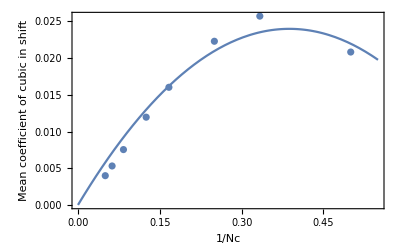

```mathematica
Show[ListPlot[cd,Axes->False,Frame->True,PlotRange->{{0,0.55},Automatic},FrameLabel->{"1/Nc","Mean coefficient of cubic in shift"}],Plot[ffcd,{x,0,.55}]]
```

Plot error as a function of shift in some random shift direction

```mathematica
maxData=2Pi;data=Block[{rd=randomDirection[]},Table[Block[{shift=x If[False,IdentityMatrix[nc^2-1][[1]],rd],sg},sg=shift.suGenerators[nc];{Norm[shift,2],Norm[IdentityMatrix[nc]+I sg-sg.sg/2!-MatrixExp[I sg],2]}],{x,0,maxData, maxData/20}]];
```

```mathematica
ff=Fit[data,{x^3,x^4,x^5},x]
```

0.0267015 x^3-0.000323406 x^4-0.000089854 x^5

```mathematica
Apply[List,ff]/.x->maxData
```

{6.6233,-0.504043,-0.879907}

```mathematica
Show[ListPlot[data],Plot[{ff,x^3/48},{x,0,maxData}]]
```

## Identity staple example, SU(3)

Special case where the sum of staples is proportional to the identity matrix.

```mathematica
diagValue=Cos[x1]+Cos[x2]+Cos[-x1-x2]
```

Cos[x1]+Cos[x2]+Cos[x1+x2]

Saddle Points

```mathematica
Solve[{D[diagValue,x1]==0,D[diagValue,x2]==0},{x1,x2}]
```

{{x1→ConditionalExpression[2 π C[1],C[1]∈ℤ],x2→ConditionalExpression[2 π C[2],C[2]∈ℤ]},{x1→ConditionalExpression[2 π C[1],C[1]∈ℤ],x2→ConditionalExpression[π+2 π C[2],C[2]∈ℤ]},{x1→ConditionalExpression[-(2 π)/3+2 π C[1],C[1]∈ℤ],x2→ConditionalExpression[-(2 π)/3+2 π C[2],C[2]∈ℤ]},{x1→ConditionalExpression[(2 π)/3+2 π C[1],C[1]∈ℤ],x2→ConditionalExpression[(2 π)/3+2 π C[2],C[2]∈ℤ]},{x1→ConditionalExpression[π+2 π C[1],C[1]∈ℤ],x2→ConditionalExpression[2 π C[2],C[2]∈ℤ]},{x1→ConditionalExpression[π+2 π C[1],C[1]∈ℤ],x2→ConditionalExpression[π+2 π C[2],C[2]∈ℤ]}}

Hessian

```mathematica
hess=Outer[D[diagValue,#1,#2]&,{x1,x2},{x1,x2}]
```

{{-Cos[x1]-Cos[x1+x2],-Cos[x1+x2]},{-Cos[x1+x2],-Cos[x2]-Cos[x1+x2]}}

```mathematica
dh=Det[hess]
```

Cos[x1] Cos[x2]+Cos[x1] Cos[x1+x2]+Cos[x2] Cos[x1+x2]

```mathematica
Block[{limit=Pi 4/3},Show[Plot3D[diagValue,{x1,-limit,limit},{x2,- limit, limit},RegionFunction->Function[{x1,x2},Block[{x3=-x1-x2},Abs[x1-x2]<2 Pi&&Abs[x1-x3]<2Pi&&Abs[x2-x3]<2 Pi]]],Graphics3D[{PointSize[0.02],Table[Point[{x1,x2,diagValue}],{x1,-4/3 Pi,2 Pi,2 Pi},{x2,-4/3 Pi,2 Pi,2 Pi}],Table[Point[{x1,x2,diagValue}],{x1,-2/3 Pi,2 Pi,2 Pi},{x2,-2/3 Pi,2 Pi,2 Pi}],Table[Point[{x1,x2,diagValue}],{x1,-Pi,Pi,Pi},{x2,-Pi,Pi,Pi}]}]]]
```

### Test saddle point routine

Run this as a group

```mathematica
sqrtU1=SUPower[u1=randomSUMatrix[3],0.25];
phi1=centerPhases[u1]
```

{0.0697439,2.72834,-2.79808}

```mathematica
{sqrtU2,maxShift}=linkSaddlePointStep[sqrtU1,sqrtU1];maxShift
```

0.0011188

```mathematica
phi2=centerPhases[sqrtU2.sqrtU1]
```

{0.0355178,1.36384,-1.39936}

```mathematica
Block[{limit=3Pi/2},Show[DensityPlot[diagValue,{x1,-limit,limit},{x2,-limit,limit},Epilog->{Thickness[0.02],Line[{Take[phi1,2],Take[phi2,2]}],PointSize[0.02],Table[Point[{y1,y2}],{y1,-4/3 Pi,2 Pi,2 Pi},{y2,-4/3 Pi,2 Pi,2 Pi}],Table[Point[{y1,y2}],{y1,-2/3 Pi,2 Pi,2 Pi},{y2,-2/3 Pi,2 Pi,2 Pi}],Table[Point[{y1,y2}],{y1,-Pi,Pi,Pi},{y2,-Pi,Pi,Pi}]}],DensityPlot[dh,{x1,-limit,limit},{x2,-limit,limit},PlotRange->{-0.1,0.1}]]]
```

## Input gauge configurations

```mathematica
<<"../data/3-3/periodic-4-7.5-3.m"
```

```mathematica
<<"../data/3-3/periodic-6-8.175-3.m"
```

```mathematica
<<"../data/3-3/periodic-22-42-1.m"
```

```mathematica
<<"../data/3-3/periodic-22-42-1-cool.m";
```

```mathematica
<<"../data/3-3/periodic-22-42-5.m"
```

```mathematica
<<"../data/3-3/periodic-22-80-5.m"
```

```mathematica
<<"../data/3-4/periodic-16-28-1.m"
```

```mathematica
<<"../data/3-4/periodic-16-33-4.m"
```

```mathematica
<<"../data/3-4/periodic-20-150-5.m"
```

```mathematica
<<"../data/3-3/winding-20-80-0-5.m"
```

```mathematica
<<"../data/3-3/winding-20-80-1-5.m"
```

```mathematica
<<"../data/3-4/winding-20-60-0-4.m"
```

```mathematica
<<"../data/3-4/winding-20-60-1-4.m"
```

```mathematica
<<"../data/3-6/periodic-18-90-1.m"
```

```mathematica
<<"../data/3-6/periodic-18-170-1.m"
```

```mathematica
{nd,nc,beta,latticeDimensions,Dimensions[gaugeField]}
```

{3,3,8.175,{6,6,6},{3,216,3,3}}

Test that links are approximately SU (N)

```mathematica
Length[badMatrices=Select[Flatten[gaugeField,1],Not[SUMatrixQ[#,1.0 10^-10]]&]]
```

0

## Plaquette distribution

The plaquette values, if rescaled to the [0,1] interval, generally fit a Beta distribution, but we can equivalently use a Gamma distribution for small lattice spacings.

```mathematica
useGammaDistribution=True;
```

```mathematica
Histogram[data=Flatten[Table[Table[(1-plaquette[dir1,dir2,latticeCoordinates[i]]/nc)/If[useGammaDistribution,1,2],{i,latticeVolume[]}],{dir1,2},{dir2,dir1+1,nd}]]]
```

```mathematica
{Mean[data],dist=FindDistribution[data,TargetFunctions->Which[useGammaDistribution,{GammaDistribution},True,{BetaDistribution},True,All]]}
```

{0.0650492,GammaDistribution[4.03725,0.0161123]}

Distribution for 1 - Tr(plaquette)/nc

```mathematica
TableForm[dm={{"nd","nc","beta","mean","alpha","beta"},{3,3,42.,0.0650492058072443,4.0372454261752875,0.016112274320900954},{3,3,80.,0.03371067322265413,4.011655372432331,0.008403182749520672},{3,4,28.,0.1923250246554901,7.7282971359028245,0.02488582171194133},{3,4,33.,0.1604205616819077,7.670953223240458,0.02091272844591148},{3,4,150.,0.03380841583718067,7.620434296041462,0.004436547121053944},{3,6,90.,0.13525994258717414,18.387360829900825,0.007356136850654697},{3,6,170.,0.07017369456939337,18.102497926494276,0.0038764647207436133}}]
```

nd | nc | beta | mean | alpha | beta
3 | 3 | 42. | 0.0650492 | 4.03725 | 0.0161123
3 | 3 | 80. | 0.0337107 | 4.01166 | 0.00840318
3 | 4 | 28. | 0.192325 | 7.7283 | 0.0248858
3 | 4 | 33. | 0.160421 | 7.67095 | 0.0209127
3 | 4 | 150. | 0.0338084 | 7.62043 | 0.00443655
3 | 6 | 90. | 0.13526 | 18.3874 | 0.00735614
3 | 6 | 170. | 0.0701737 | 18.1025 | 0.00387646

```mathematica
Fit[Log[Map[#[[{2,3,5}]]&,Rest[dm]]],{1,x,y},{x,y}]
```

-0.957013+2.19225 x-0.0130246 y

```mathematica
alphaf=Fit[Map[#[[{2,3,5}]]&,Rest[dm]],{x,x^2,x^2/y},{x,y}]
```

-0.383726 x+0.567826 x^2+(0.336766 x^2)/y

```mathematica
Fit[Log[Map[#[[{2,3,6}]]&,Rest[dm]]],{1,x,y},{x,y}]
```

-0.276496-0.00344917 x-1.02658 y

```mathematica
betaf=Fit[Map[#[[{2,3,6}]]&,Rest[dm]],{1/y,1/(x y),1/y^2},{x,y}]
```

1.27185/y^2+0.655795/y-0.0190906/(x y)

```mathematica
Series[alphaf betaf,{y,Infinity,2},{x,Infinity,-1}]
```

(0.372377 x^2-0.262486 x+O[1/x]^0)/y+(0.943037 x^2-0.49447 x+O[1/x]^0)/y^2+O[1/y]^3

```mathematica
dist=GammaDistribution[nc^2/2,2/(3 beta)]
```

GammaDistribution[9/2,0.015873]

```mathematica
Mean[GammaDistribution[a1,b1]]
```

a1 b1

```mathematica
TableForm[Map[{#[[2]],#[[3]],#[[4]],#[[2]]^2/(3 #[[3]]),#[[2]]^4/(#[[3]]^2 2 Pi)}&,dm]]
```

nc | beta | mean | nc^2/(3 beta) | nc^4/(2 beta^2 π)
3 | 42. | 0.0650492 | 0.0714286 | 0.00730814
3 | 80. | 0.0337107 | 0.0375 | 0.0020143
4 | 28. | 0.192325 | 0.190476 | 0.051969
4 | 33. | 0.160421 | 0.161616 | 0.0374138
4 | 150. | 0.0338084 | 0.0355556 | 0.00181083
6 | 90. | 0.13526 | 0.133333 | 0.0254648
6 | 170. | 0.0701737 | 0.0705882 | 0.00713719

```mathematica
Block[{width=0.0025},Show[Histogram[data,{width},Axes->False,Frame->True],Plot[Length[data] width PDF[dist][x],{x,0,3 Mean[data]}]]]
```

## Gauge Invariant Shifts

The gauge transforms should leave the action invariant.  Thus any small shift in the direction of a gauge transform should have zero gradient and zero second derivative.

Orthogonalizing the associated matrix creates a matrix that is roughly 50% dense.  This seems to be independent of the basis ordering.  For instance, going to checkerboard (linearSiteIndex[]) just changes the sparsity pattern.

```mathematica
<<"../data/3-3/periodic-4-7.5-3.m"
```

```mathematica
<<"../data/3-3/periodic-6-8.175-3.m"
```

```mathematica
<<"../data/3-3/periodic-22-42-1.m"
```

Create trivial lattice with one non-trivial link.

```mathematica
nd=3;nc=2;latticeDimensions={2,1,1};
If[True,makeTrivialLattice[randomGauge->False];setLink[2,{1,1,1},MatrixExp[I Pi RandomReal[] suGenerators[][[1]]]],gaugeField=Table[If[dir==1,{{0,1},{1,0}},IdentityMatrix[nc]],{dir,nd},{latticeVolume[]}];Clear[linearSiteIndex];
Do[linearSiteIndex[latticeCoordinates[i]]=i,{i,latticeVolume[]}]];averagePlaquette[]
```

0.864238

Create random lattice :

```mathematica
nd=3;nc=2;latticeDimensions={2,2,2};gaugeField=Table[randomSUMatrix[],{nd},{latticeVolume[]}];Clear[linearSiteIndex];Do[linearSiteIndex[latticeCoordinates[i]]=i,{i,latticeVolume[]}];averagePlaquette[]
```

-0.0777437

Timing, matrix size, density, and memory use:
See https://mathematica.stackexchange.com/questions/83721/what-are-sparsearray-properties-how-and-when-should-they-be-used

```mathematica
Timing[rl=Chop[makeRootLattice[]];
{Dimensions[sh=Chop[gaugeTransformShifts[rl]]],sh[Density],printMemory[sh]}]
```

{0.054461,{{512,1536},0.03125,792.×10^3}}

### Look at sh.Transpose[sh] and distribution of right hand sides

```mathematica
{vals,oo}=Eigensystem[Normal[sh.Transpose[sh]]];Dimensions[oo]
```

{1728,1728}

The matrix is fairly well-conditioned.
get 10.5 for data/3-3/periodic-6-8.175-3.m
get 24 for 3-4/periodic-16-33-4.m

```mathematica
condition[sh.Transpose[sh]]
```

10.5141

Convergence of conjugate gradients for this matrix is this to the number of steps:
get 0.52 for data/3-3/periodic-6-8.175-3.m
and 0.66 for second case

```mathematica
(Sqrt[%]-1)/(Sqrt[%]+1)
```

0.528585

```mathematica
Histogram[vals,30,PlotRange->{{0,Floor[Max[vals]+1]},All}]
```

Generate and store values of shifts, using flag “storeBB”

```mathematica
latticeSaddlePointStep[storePairs->True,fixedDir->0,Method->"MINRES",largeShiftSearch->300,storeBB->True];Dimensions[bb0]
```

dynamicPart memory:  1.56×10^6, gaugeTransform shifts 1.34×10^6 (bytes) for Automatic

Exit ersatzLanczos.  istop=6 itn=600

Exit ersatzLanczos.  Anorm=2.63126

Exit ersatzLanczos.  time (seconds): M=0, A=0.967, orthogonalization=2.76, total=3.89204

Exit ersatzLanczos.  The iteration limit was reached

cutoffNullSpace:  18 of 300 zeros

Exit minres.  istop=1 itn=1542

Exit minres.  Anorm=105.741 Acond=2.1662

Exit minres.  rnorm=1.19031×10^-10 ynorm=100.063

Exit minres.  Arnorm=1.54669×10^-10

Exit minres.  time (seconds): M=0, A=2.8, orthogonalization=16.1, total=26.02348

Exit minres.  A solution to Ax=b was found, given rtol

findDelta.  time (seconds):  dynamic part=2.36, small shifts=0.33, A=0.92, total=30.26491

applyCutoff2: rescale maxNorm 8.39407 to 2

times:  {8.61,10.23922,30.90546,0.06479}

{2145,5184}

Average overlap of b-vectors with each eigenvector of sh.Transpose[sh], eigenvectors are sorted by decreasing eigenvalue.

```mathematica
ListPlot[Map[Norm[#,1]&,oo.sh.Transpose[Drop[bb0/Map[Norm,bb0],600]]],PlotRange->All]
```

```mathematica
ListPlot[Map[Norm[#,1]&,oo.sh.Transpose[Orthogonalize[Drop[bb0,600]]]],PlotRange->All]
```

Overlap of b-vectors with subspace remains large over iterations.

```mathematica
ListPlot[Map[Norm,bb0.Transpose[sh]]]
```

Fraction of independence of each b-vector from all previous b-vectors after transforming into the gauge transform space.  We see that the vectors are nearly orthogonal, to start with.  Note that the first iterations are for the calculation that locates the large shift eigenvectors of the Hessian.  Then comes the iterations associated with finding  the actual shifts.

```mathematica
gbb0=Take[bb0,600].Transpose[sh];
```

```mathematica
overlaps=Chop[Block[{obb=If[False,gbb0/Map[Norm,gbb0],Orthogonalize[gbb0]]},Table[Block[{b=gbb0[[i]]},b=b/Norm[b];Do[Block[{ob=obb[[j]]},b=b-(ob.b) ob],{j,i-1}];Norm[b]],{i,Length[gbb0]}]],10^-7];
```

```mathematica
ListPlot[overlaps]
```

### Compare different dynamicPart[ ] methods.

Verify that this is equal to the NullSpace[ ] used in the dense calculation.

```mathematica
Block[{nsh=NullSpace[sh],tvec=RandomReal[1,Length[First[sh]]]},Norm[dynamicPart[sh][tvec]-Transpose[nsh].nsh.tvec]]
```

dynamicPart memory:  0., gaugeTransform shifts 792.×10^3 (bytes) for Automatic

1.79231×10^-11

```mathematica
testProjection[f_]:=Block[{r1=RandomReal[1,{Length[First[sh]]}],r2,t1=SessionTime[]},r2=f[r1];Print["timing:  ",SessionTime[]-t1, " s"];{Norm[r2-f[r2]],Norm[sh.r2]}]
```

```mathematica
Timing[(dpOrtho=dynamicPart[sh]);]
```

dynamicPart memory:  0., gaugeTransform shifts 792.×10^3 (bytes) for Automatic

{0.001099,Null}

```mathematica
testProjection[dpOrtho]
```

timing:  0.06867 s

{1.79119×10^-11,2.74451×10^-11}

```mathematica
Timing[(dpLeast=dynamicPart[sh,Method->"LeastSquares"]);]
```

dynamicPart memory:  793.×10^3, gaugeTransform shifts 792.×10^3 (bytes) for LeastSquares

{0.003181,Null}

```mathematica
testProjection[dpLeast]
```

timing:  0.0616 s

{1.03705×10^-15,7.12166×10^-7}

```mathematica
Timing[(dpLinear=dynamicPart[sh,Method->"LinearSolve"]);]
```

dynamicPart memory:  465.×10^3, gaugeTransform shifts 792.×10^3 (bytes) for LinearSolve

{0.069831,Null}

For 3-3/periodic-22, 182s, 77MB memory, gaugeTransformShifts 132MB, trouble converging.  Looks like the Krylov method just stores the matrix until solving.

```mathematica
Timing[(dpLinear=dynamicPart[sh,Method->{"LinearSolve",Method->{"Krylov","Method"->"ConjugateGradient","Tolerance"->10^-9}}]);]
```

dynamicPart memory:  465.×10^3, gaugeTransform shifts 792.×10^3 (bytes) for LinearSolve

{0.013464,Null}

```mathematica
testProjection[dpLinear]
```

timing:  0.03618 s

{7.64923×10^-9,1.65653×10^-8}

```mathematica
Timing[dpzLinear=dynamicPart[sh,Method->{"MINRES",printDetails->1,rTolerance->10^-10}];]
```

dynamicPart memory:  0., gaugeTransform shifts 792.×10^3 (bytes) for MINRES

{0.000991,Null}

Faster than built-in Conjugate gradients, perhaps because we don’t explicitly construct the matrix.

```mathematica
testProjection[dpzLinear]
```

Exit minres.  istop=1 itn=30

Exit minres.  Anorm=48.6756 Acond=1.63858

Exit minres.  rnorm=2.34096×10^-8 ynorm=6.00578

Exit minres.  Arnorm=2.26899×10^-7

Exit minres.  time (seconds): M=0, A=0.0366, orthogonalization=0, total=0.04536

Exit minres.  A solution to Ax=b was found, given rtol

timing:  0.0474 s

Exit minres.  istop=1 itn=30

Exit minres.  Anorm=37.7571 Acond=1.16623

Exit minres.  rnorm=3.62162×10^-17 ynorm=1.20024×10^-8

Exit minres.  Arnorm=4.1842×10^-16

Exit minres.  time (seconds): M=0, A=0.0289, orthogonalization=0, total=0.03495

Exit minres.  A solution to Ax=b was found, given rtol

{1.57052×10^-8,2.34096×10^-8}

### Improve sparsity of gauge invariant shift matrix

```mathematica
MatrixPlot[sh]
```

Orthonormal basis of gauge transforms.  We see that we get roughly 50% sparsity.

```mathematica
MatrixPlot[osh=SparseArray[Chop[Orthogonalize[sh]]]]
```

```mathematica
osh[Density]
```

0.557613

```mathematica
lastZero[x_]:=Block[{j=None},Do[If[x[[i]]==0,j=i],{i,Length[x]}];j]
```

Try to sort rows so that Orthogonalize[..] is more sparse.  This essentially didn’t work.

Octahedral plus tetrahedral tessellation of the lattice.

```mathematica
Clear[allPlanes];allPlanes[]:=allPlanes[nd];allPlanes[nd_]:=allPlanes[nd]=Table[2*BitAnd[1,BitShiftRight[i-1,j-1]]-1,{i,2^(nd-1)},{j,nd}]
```

Cubic tessellation of the lattice

```mathematica
Clear[allPlanes];allPlanes[]:=allPlanes[nd];allPlanes[nd_]:=allPlanes[nd]=IdentityMatrix[nd]
```

```mathematica
coordRank[coords_]:=coordRank[coords,Total[latticeDimensions]];coordRank[coords_,top_]:=Block[{cc=allPlanes[].coords,i=1},While[AnyTrue[Mod[cc,2^i],#==0&]&&2^i<top,i+=1];If[True (* For debugging *),(i-1)*Length[cc]+lastZero[Mod[cc,2^(i-1)]],{i,Mod[cc,2^(i-1)]}]]
```

```mathematica
TableForm[Table[coordRank[{4,i,j},3*16],{i,16},{j,16}],TableDepth->2]
```

12 | 4 | 22 | 4 | 24 | 4 | 10 | 4 | 12 | 4 | 17 | 4 | 19 | 4 | 10 | 4
4 | 22 | 4 | 8 | 4 | 24 | 4 | 8 | 4 | 17 | 4 | 8 | 4 | 19 | 4 | 8
22 | 4 | 12 | 4 | 10 | 4 | 24 | 4 | 17 | 4 | 12 | 4 | 10 | 4 | 19 | 4
4 | 8 | 4 | 12 | 4 | 8 | 4 | 24 | 4 | 8 | 4 | 12 | 4 | 8 | 4 | 19
23 | 4 | 10 | 4 | 12 | 4 | 17 | 4 | 24 | 4 | 10 | 4 | 12 | 4 | 18 | 4
4 | 23 | 4 | 8 | 4 | 17 | 4 | 8 | 4 | 24 | 4 | 8 | 4 | 18 | 4 | 8
10 | 4 | 23 | 4 | 17 | 4 | 12 | 4 | 10 | 4 | 24 | 4 | 18 | 4 | 12 | 4
4 | 8 | 4 | 23 | 4 | 8 | 4 | 12 | 4 | 8 | 4 | 24 | 4 | 8 | 4 | 12
12 | 4 | 17 | 4 | 23 | 4 | 10 | 4 | 12 | 4 | 18 | 4 | 24 | 4 | 10 | 4
4 | 17 | 4 | 8 | 4 | 23 | 4 | 8 | 4 | 18 | 4 | 8 | 4 | 24 | 4 | 8
17 | 4 | 12 | 4 | 10 | 4 | 23 | 4 | 18 | 4 | 12 | 4 | 10 | 4 | 24 | 4
4 | 8 | 4 | 12 | 4 | 8 | 4 | 23 | 4 | 8 | 4 | 12 | 4 | 8 | 4 | 24
20 | 4 | 10 | 4 | 12 | 4 | 18 | 4 | 23 | 4 | 10 | 4 | 12 | 4 | 21 | 4
4 | 20 | 4 | 8 | 4 | 18 | 4 | 8 | 4 | 23 | 4 | 8 | 4 | 21 | 4 | 8
10 | 4 | 20 | 4 | 18 | 4 | 12 | 4 | 10 | 4 | 23 | 4 | 21 | 4 | 12 | 4
4 | 8 | 4 | 20 | 4 | 8 | 4 | 12 | 4 | 8 | 4 | 23 | 4 | 8 | 4 | 12

```mathematica
checkerboardRank[]:=Block[{y=Array[Null&,{nGauge[0]}],gindex},Do[Block[{coords=latticeCoordinates[i]},gindex=coords2gauge[0][coords,ca];y[[gindex]]={ca+(nc^2-1)coordRank[coords],gindex}],{i,latticeVolume[]},{ca,nc^2-1}];Map[#[[2]]&,Sort[y]]]
```

```mathematica
osh2=SparseArray[Chop[Orthogonalize[sh[[checkerboardRank[]]]]]]
```

```mathematica
MatrixPlot[osh2]
```

```mathematica
osh2[Density]
```

0.398526

```mathematica
MatrixPlot[sshh=Chop[sh.Transpose[sh]]]
```

```mathematica
sshh[Density]
```

0.0283565

### Dynamic space projection properties

Transpose[sh].sh is symmetric positive semi-definite.  The null space corresponds to non-gauge shifts.  Note that Transpose[sh].sh is still quite sparse.

```mathematica
ListPlot[Sort[Eigenvalues[Normal[Transpose[sh].sh]]]]
```

Test that the gradients are orthogonal to all gauge transforms.

```mathematica
Tally[Chop[sh.grad0]]
```

{{0,6}}

However, since the Hessian is quadratic in the shifts, it is not necessarily in the direction of two infinitesimal gauge transforms.

```mathematica
MatrixPlot[Chop[sh.hess0.Transpose[sh]]]
```

Project onto subspace of physical degrees of freedom, this results in a dense matrix.

```mathematica
MatrixPlot[Chop[proj=NullSpace[sh]]]
```

### Adjoint trace identity

Verify unitarity of the adjoint color matrix for some random element of SU(nc):  
        2 Tr[u.suGenerator[a].ConjugateTranspose[u].suGenerator[b]].  
Also, this matrix should be real-valued.  This matrix comes up in the analytic calculations.

```mathematica
Block[{nc=3,u},u=randomSUMatrix[];ff=Chop[Outer[2 Tr[u.#1.ConjugateTranspose[u].#2]&,suGenerators[],suGenerators[],1]];ff2=Chop[Outer[2 Tr[u.u.#1.ConjugateTranspose[u.u].#2]&,suGenerators[],suGenerators[],1]];]
```

```mathematica
Chop[ff.ConjugateTranspose[ff]]
```

{{1.,0,0,0,0,0,0,0},{0,1.,0,0,0,0,0,0},{0,0,1.,0,0,0,0,0},{0,0,0,1.,0,0,0,0},{0,0,0,0,1.,0,0,0},{0,0,0,0,0,1.,0,0},{0,0,0,0,0,0,1.,0},{0,0,0,0,0,0,0,1.}}

```mathematica
Tally[Flatten[Chop[ff.ff-ff2]]]
```

{{0,64}}

## Lattice stationary point

### Trivial lattice

```mathematica
nd=3;nc=5;latticeDimensions={2,2,2};
makeTrivialLattice[randomGauge->True];averagePlaquette[]
```

1.

```mathematica
libGaugeField=latticeSaddlePointStep[storePairs->True,fixedDir->0];
```

cutoff:  1000000

times:  {3.09,3.40822,0.34524,0.00464}

Symmetries of the lattice action.   Gauge fixing removes one dimension worth.  Difference is 9 for SU(2), 24 for SU(3), 45 for SU(4), 72 for SU(5), independent of the size of the lattice.  In general, the difference is 3 (nc^2-1).

Also, all curvatures are negative, indicating that this a a local minimum of the action, since the action is 1-Re(Tr(plaquettte))/Nc.

The result is independent of gauge choice.

```mathematica
{Length[proj0[[1]]],Length[proj0[[1]]]/nd}
```

{576,192}

Zero curvature would indicate a gauge symmetry.

```mathematica
Tally[Rationalize[Chop[pairs0]]]
```

{{{-6,0},48},{{-4,0},144},{{-2,0},144},{{0,0},72}}

### Compare different strategies.

```mathematica
<<"../data/3-3/periodic-4-7.5-3.m"
```

```mathematica
<<"../data/3-3/periodic-6-8.175-3.m"
```

```mathematica
cutoff=Min[Pi .01^(1/3),Sqrt[1-averagePlaquette[]]]
```

0.634944

Find fraction of shift that is non-gauge transformation.

```mathematica
Dimensions[dynamicShifts=NullSpace[gp=gaugeTransformShifts[makeRootLattice[]]]]
```

{3456,5184}

```mathematica
gaugeFieldAll=latticeSaddlePointStep[storePairs->True,fixedDir->-1];pairsAll=pairs0;ooprojAll=oo0.proj0;
```

applyCutoff3:  282 of 5184 zeros

applyCutoff2: rescale maxNorm 8.84035 to 2.

times:  {8.18,9.774267,22.73788,0.06974}

```mathematica
(Norm[dynamicShifts.#]/Norm[#])&[grad0]
```

1.

On lattices with more than one link in each direction, the diagonal is zero.  But off-diagonal elements are non-zero since the quadratic expansion violates gauge invariance.

```mathematica
Tr[gp.hess0.Transpose[gp]]
```

1.01377×10^-13

```mathematica
gaugeFieldDynamic=latticeSaddlePointStep[storePairs->True,fixedDir->0];pairsDynamic=pairs0;ooprojDynamic=oo0.proj0;
```

applyCutoff3:  133 of 3456 zeros

applyCutoff2: rescale maxNorm 5.15131 to 2.

times:  {8.38,10.06802,32.77853,0.0634}

Map to the shift on the full lattice:

```mathematica
ffdd=2;Dimensions[axialProj=Block[{proj=Association[],i,j},Do[Block[{coords=latticeCoordinates[i]},proj[{coords2grad[ffdd][dir,coords,k],coords2grad[-1][dir,coords,k]}]=1],{dir,nd},{i,latticeVolume[]},{k,nc^2-1}];SparseArray[Normal[proj]]]]
```

{1152,1536}

```mathematica
setAxialGauge[ffdd]
```

```mathematica
gaugeFieldAxial=latticeSaddlePointStep[storePairs->True,fixedDir->ffdd];pairsAxial=pairs0;ooprojAxial=oo0.proj0.axialProj;
```

cutoff:  1

applyCutoff3 zeros: {16,1152}

applyCutoff2 rescale: {13.1624,1}

times:  {2.18,2.51081,0.31219,0.01825}

#### Distribution of shifts

Need to turn on switch in function applyCutoff3 to accumulate data for this plot.

```mathematica
ListPlot[{Map[{#[[1]],Abs[#[[2]]]}&,goodPairs0],Map[{#[[1]],Abs[#[[2]]]}&,badPairs0]},Axes->False,Frame->True]
```

```mathematica
ListPlot[Map[{#[[1]],Abs[#[[2]]]}&,pairsDynamic],Axes->False,Frame->True]
```

```mathematica
Histogram[{Map[First,pairsAll],Map[First,pairsAxial],Map[First,pairsDynamic]}]
```

Note that a Cauchy Distribution is generated by the ratio of two normally distributed variables.

```mathematica
fitt=FindDistribution[Map[#[[2]]/#[[1]]&,pairsDynamic]]
```

CauchyDistribution[-0.00445658,0.301532]

```mathematica
Block[{w=0.2,max=2},Show[Histogram[Map[#[[2]]/#[[1]]&,pairsDynamic],{w},Axes->False,Frame->True,PlotRange->{{-max,max},All}],Plot[PDF[fitt,x]Length[pairsDynamic] w,{x,-max,max},PlotRange->All]]]
```

We see that there is a good fit in the tails and at the peak.

```mathematica
Block[{w=0.2,data=Map[Abs[#[[2]]/#[[1]]]&,pairsDynamic]},Show[Histogram[data,{"Log",{w}},ScalingFunctions->"Log",Axes->False,Frame->True,PlotRange->All],LogPlot[ 2(CDF[fitt,Exp[x] 10^(w/2)]-CDF[fitt,Exp[x]10^(-w/2)])Length[data],{x,Log[Min[data]],Log[Max[data]]},PlotRange->All]]]
```

```mathematica
Histogram[{Map[#[[2]]/#[[1]]&,pairsAll],Map[#[[2]]/#[[1]]&,pairsAxial],Map[#[[2]]/#[[1]]&,pairsDynamic]},{0.1},PlotRange->{{-2,2},Automatic},Axes->False,Frame->True,PlotRange->All]
```

#### Compare shift vectors

```mathematica
cosAngle[a_,b_]:=a.b/(Norm[a] Norm[b])
```

```mathematica
Clear[shifts];makeShifts[type_,pairs_,ooproj_]:=(shifts[type,0,0]=-Map[#[[2]]/#[[1]]&,pairs].ooproj;
shifts[type,1,0]=-Apply[applyCutoff3[##,ooproj,1]&,Transpose[pairs]].ooproj;
shifts[type,0,1]=applyCutoff2[shifts[type,0,0]];
shifts[type,1,1]=applyCutoff2[shifts[type,1,0]];)
```

```mathematica
Print["starting All"];
makeShifts["All",pairsAll,ooprojAll];
Print["starting Dynamic"];makeShifts["Dynamic",pairsDynamic,ooprojDynamic];
Print["starting Axial"];makeShifts["Axial",pairsAxial,ooprojAxial];
```

starting All

applyCutoff3:  70 of 1536 zeros

applyCutoff2: rescale maxNorm 256.13 to 1

applyCutoff2: rescale maxNorm 8.26844 to 1

starting Dynamic

applyCutoff3:  32 of 1024 zeros

applyCutoff2: rescale maxNorm 48.3877 to 1

applyCutoff2: rescale maxNorm 6.31072 to 1

starting Axial

applyCutoff3:  48 of 1152 zeros

applyCutoff2: rescale maxNorm 303.041 to 1

applyCutoff2: rescale maxNorm 6.7566 to 1

```mathematica
typeOuter[type_]:=Block[{sh={shifts[type,0,0],shifts[type,1,0],shifts[type,0,1],shifts[type,1,1]}},TableForm[Outer[cosAngle,sh,sh,1]]]
```

```mathematica
typeOuter["All"]
```

1. | 0.0291846 | 1. | 0.0291846
0.0291846 | 1. | 0.0291846 | 1.
1. | 0.0291846 | 1. | 0.0291846
0.0291846 | 1. | 0.0291846 | 1.

```mathematica
typeOuter["Dynamic"]
```

1. | 0.108593 | 1. | 0.108593
0.108593 | 1. | 0.108593 | 1.
1. | 0.108593 | 1. | 0.108593
0.108593 | 1. | 0.108593 | 1.

```mathematica
typeOuter["Axial"]
```

1. | 0.0255151 | 1. | 0.0255151
0.0255151 | 1. | 0.0255151 | 1.
1. | 0.0255151 | 1. | 0.0255151
0.0255151 | 1. | 0.0255151 | 1.

```mathematica
cosAngle[shifts["All",1,1],shifts["Dynamic",1,1]]
```

0.286411

```mathematica
cosAngle[shifts["Dynamic",1,1],shifts["Axial",1,1]]
```

0.0341957

```mathematica
cosAngle[shifts["All",1,1],shifts["Axial",1,1]]
```

0.086668

```mathematica
TableForm[Table[(Norm[dynamicShifts.#]/Norm[#])&[shifts["All",i,j]],{i,0,1},{j,0,1}]]
```

0.396732 | 0.396732
0.582136 | 0.582136

```mathematica
TableForm[Table[(Norm[dynamicShifts.#]/Norm[#])&[shifts["Dynamic",i,j]],{i,0,1},{j,0,1}]]
```

1. | 1.
1. | 1.

```mathematica
TableForm[Table[(Norm[dynamicShifts.#]/Norm[#])&[shifts["Axial",i,j]],{i,0,1},{j,0,1}]]
```

0.78487 | 0.78487
0.798573 | 0.798573

```mathematica
Tally[Chop[Flatten[dynamicShifts.Transpose[dynamicShifts]-IdentityMatrix[1024]]]]
```

{{0,1048576}}

```mathematica
Histogram[shifts["Dynamic",1,1],{.05}]
```

## Junk

```mathematica
phases=centerPhases[centerSUMatrix[1,3]]
```

{(2 π)/3,(2 π)/3,-(4 π)/3}

```mathematica
N[phases,16]
```

{2.094395102393195,2.094395102393195,-4.188790204786391}

```mathematica
Chop[lineLinks[1,{2,3,4}]]
```

```mathematica
plotAction[1,2,3,{1,1,1},{0,4 nc^2/3}]
```

```mathematica
latticeSaddlePoint[5]
```

```mathematica
stats=latticeSaddlePoint[50]
```

```mathematica
ListLogPlot[Map[#[[{1,3}]]&,stats]]
```

```mathematica
ListLogPlot[Map[{#[[1]],norm/.#[[4]]["BestFitParameters"]}&,stats]]
```

```mathematica
ListLogPlot[Map[{#[[1]],aw/.#[[4]]["BestFitParameters"]}&,stats]]
```

```mathematica
stats=latticeSaddlePoint[14]
```

Save resulting lattice

```mathematica
Save["periodic-3-3-22-42-1-fastcool.m",{nd,nc,beta,latticeDimensions,latticeLayout,gaugeField,linearSiteIndex}]
```